# Simulate Audio for Conversations with Different Arrangements of Speakers TitleYour essay title should be concise, descriptive and easy to understand. ◼ Choose a subject that you know well. ◼ Be as straightforward as possible. ◼ Be specific, distinctive and informative. ◼ Clearly convey the subject of the essay. ◼ Make sure the subject area is recognizable by non-experts. ◼ Avoid ambiguous abbreviations. ◼ Avoid overly broad titles. Examples: Visualizing the Collatz Conjecture Euclidean Vectors Networks Represented as Graphs Morphological Image Segmentation

AuthorInclude full name and credentials for all authors.Click for more informationShubham Kumar

AbstractAn abstract summarizes the most important points in your essay.
	◼ Summarize your most important content in about 100 words.
	◼ Provide a concise overview of the essay's conversation.
	◼ Highlight the motivations and scope.
	◼ Pay attention to the target audience.

Example:
Public-key cryptography, also known as asymmetric cryptography, uses two different but mathematically linked keys, one public and one private. In Rivest–Shamir–Adleman (RSA) cryptography, both the public and the private keys can encrypt a message; the opposite key from the one used to encrypt a message is used to decrypt it. Using RSA, we show how to encrypt messages between two users.
Click for more information

## SectionHeaderInfoButtonA proper heading structure helps to organize your content for readability. ◼ Categorize sections based on similar content. ◼ Each section should tell a story by itself. ◼ Headings overall should tell the outline of the essay. Examples: The Central Limit Theorem Discovering the Central Limit Theorem The Normal Distribution Toward the Normal Distribution The Normal Distribution in 2D and Beyond Random Walks What Is Not a Normal Distribution Collapse Models Collapse Problem in Quantum Random Processes Collapse as a Dynamical Random Process Recovering Quantum after Statistical Averaging Drawbacks of Collapse Models Click for more informationIntroduction to Spatial Audio

#### Sound Localization

TopicSentenceInfoButtonDescribe your concepts in a few sentences of text.
	◼ Text describes the flow of conversation.
	◼ It clarifies the transition from one segment to the next one.
	◼ It should explain how the topic is studied and (broadly) how the topic is implemented in the code.Click for more informationNeuroscientists have discovered that the azimuth of a sound in an ideal anechoic space can be determined by one's brain with two primary binaural parameters. Namely, the difference in arrival time between each ear and the relative amplitude of high-frequency sounds after attenuation [footnote]. The former can be modeled quite easily and yields consistent results.

#### Approaching the Problem

CodeTextInfoButtonDescribe your concepts in a few sentences of text.
	◼ Text describes the flow of conversation.
	◼ It clarifies the transition from one segment to the next one.
	◼ It should explain how the topic is studied and (broadly) how the topic is implemented in the code.

Examples:
	Find the eigenvalues:
	A function that generates a two-dimensional graphic of an n x m array of cells with value 1:Click for more informationVisualizing a space containing a single sound source and two ears:

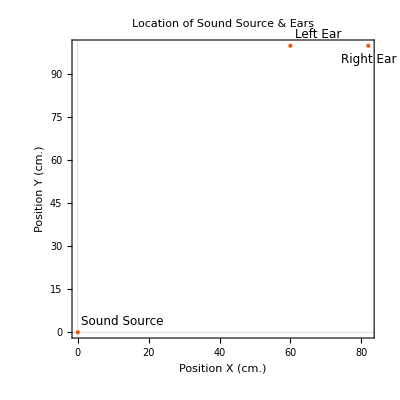

```mathematica
PlotPoint2dAudio[]
```

TopicSentenceInfoButtonDescribe your concepts in a few sentences of text.
	◼ Text describes the flow of conversation.
	◼ It clarifies the transition from one segment to the next one.
	◼ It should explain how the topic is studied and (broadly) how the topic is implemented in the code.Click for more informationThe delay of sound perception in either ear can be computed using the distance and speed of sound. Once the delay is determined, the timing of the audio can be shifted in both stereo channels to effectively simulate audio originating from a sound source at some distance away.

CodeTextInfoButtonDescribe your concepts in a few sentences of text.
	◼ Text describes the flow of conversation.
	◼ It clarifies the transition from one segment to the next one.
	◼ It should explain how the topic is studied and (broadly) how the topic is implemented in the code.

Examples:
	Find the eigenvalues:
	A function that generates a two-dimensional graphic of an n x m array of cells with value 1:Click for more informationImplementation of Described Algorithm:

```mathematica
Point2dAudio[audioObject_, speakerPoint_, leftEar_, rightEar_]:=
Module[{f=audioObject, s=speakerPoint, le=leftEar, re=rightEar},
(*Trimming Raw Audio & Separating Audio for each Channel*)
leftA = AudioPan[f, -1.];
rightA= AudioPan[f, 1.];

(*Calculating Delays*)
leftDist = Quantity[√((le[[1]]-s[[1]])^2.+(le[[2]]-s[[2]])^2.), "centimeters"];
rightDist = Quantity[√((re[[1]]-s[[1]])^2.+(re[[2]]-s[[2]])^2.), "centimeters"];
c = StandardAtmosphereData[Quantity[0, "feet"],"SoundSpeed"];
leftDelay = leftDist/c;
rightDelay = rightDist/c;

(*Debug*)
Print["Left Ear Distance:"]; Print[leftDist];
Print["Right Ear Distance:"]; Print[rightDist];
Print["Left Ear Delay:"]; Print[leftDelay];
Print["Right Ear Delay:"]; Print[rightDelay];

(*Audio Delaying*)
leftDelayA = AudioDelay[leftA, leftDelay];
rightDelayA = AudioDelay[rightA, rightDelay];

(*Mixing to Generate Final Sound*)
AudioNormalize[AudioChannelCombine[{leftDelayA, rightDelayA}]]
]
```

CodeTextInfoButtonDescribe your concepts in a few sentences of text.
	◼ Text describes the flow of conversation.
	◼ It clarifies the transition from one segment to the next one.
	◼ It should explain how the topic is studied and (broadly) how the topic is implemented in the code.

Examples:
	Find the eigenvalues:
	A function that generates a two-dimensional graphic of an n x m array of cells with value 1:Click for more informationOriginal audio and the processed audio:

```mathematica
originalAudio = AudioTrim[Import[],{1,45}]
```

```mathematica
delayedAudio = Point2dAudio[originalAudio,{0,0},{60,100},{82,100}]
```

Left Ear Distance:

116.619 cm

Right Ear Distance:

129.321 cm

Left Ear Delay:

0.00342705 s

Right Ear Delay:

0.00380033 s

CodeTextInfoButtonDescribe your concepts in a few sentences of text.
	◼ Text describes the flow of conversation.
	◼ It clarifies the transition from one segment to the next one.
	◼ It should explain how the topic is studied and (broadly) how the topic is implemented in the code.

Examples:
	Find the eigenvalues:
	A function that generates a two-dimensional graphic of an n x m array of cells with value 1:Click for more informationConfirming that the audio has been delayed using a plot:

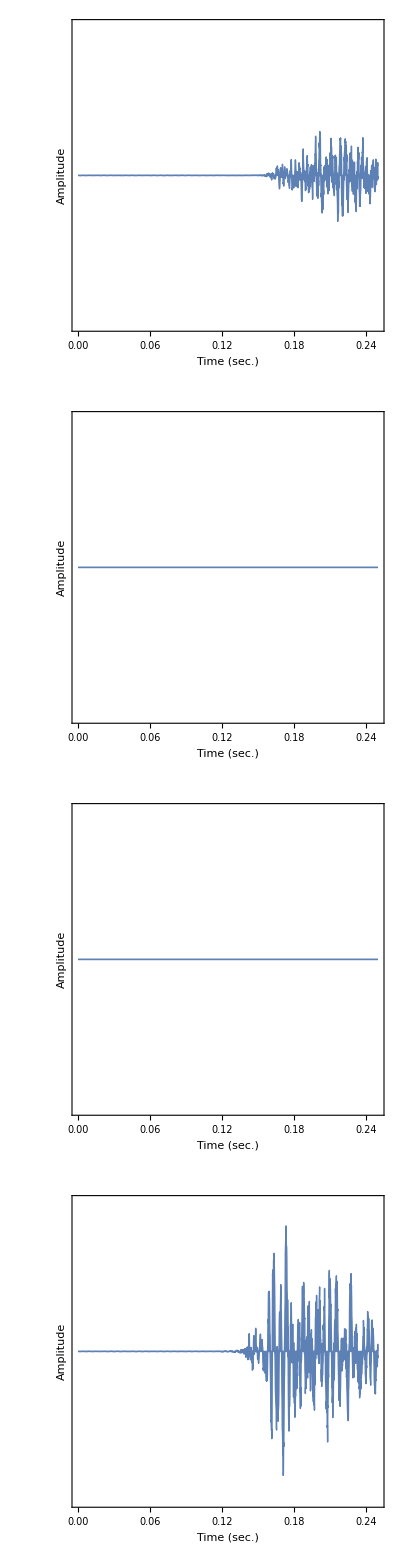

```mathematica
AudioPlot[delayedAudio,PlotRange->{{0.,0.25},{-0.1,0.1}},]
```

#### Motivation to Utilize Acoustic Modeling

TopicSentenceInfoButtonDescribe your concepts in a few sentences of text.
	◼ Text describes the flow of conversation.
	◼ It clarifies the transition from one segment to the next one.
	◼ It should explain how the topic is studied and (broadly) how the topic is implemented in the code.Click for more informationWhile the audio from the algorithm seems promising, it isn't truly a representation of reality. One of the shortcomings that is immediately obvious is the lack of attenuation. Ideally as the listener distances themself from the sound source, the amplitude should reduce. This doesn't happen with the current model since it only channels delayed audio into each ear. Although introducing an attenuation coefficient computed based on distance is feasible, modeling the inverse square law [footnote] reduction can become complicated. However, let's assume that the amplitude reduction is implemented successfully. Consider the case where the sound source, and both ears are collinear. The head would effectively serve as an obstacle or boundary preventing the sound from reaching one of the ears, thereby reducing the amplitude more than what would've been computed with the inverse square law. The field of acoustics offers the necessary tools to address some of the aforementioned limitations.

## SectionHeaderInfoButtonA proper heading structure helps to organize your content for readability. ◼ Categorize sections based on similar content. ◼ Each section should tell a story by itself. ◼ Headings overall should tell the outline of the essay. Examples: The Central Limit Theorem Discovering the Central Limit Theorem The Normal Distribution Toward the Normal Distribution The Normal Distribution in 2D and Beyond Random Walks What Is Not a Normal Distribution Collapse Models Collapse Problem in Quantum Random Processes Collapse as a Dynamical Random Process Recovering Quantum after Statistical Averaging Drawbacks of Collapse Models Click for more informationModeling Acoustics in the Time Domain

TopicSentenceInfoButtonDescribe your concepts in a few sentences of text.
	◼ Text describes the flow of conversation.
	◼ It clarifies the transition from one segment to the next one.
	◼ It should explain how the topic is studied and (broadly) how the topic is implemented in the code.Click for more informationThe mathematical model that governs waves in classical physics is a second-order linear partial differential equation, conveniently called the Wave Equation. Solving this equation using NDSolveValue yields an Interpolation Function that takes in positional arguments and a time argument and returns the corresponding pressure.

#### Obtaining the Interpolation Function

CodeTextInfoButtonDescribe your concepts in a few sentences of text.
	◼ Text describes the flow of conversation.
	◼ It clarifies the transition from one segment to the next one.
	◼ It should explain how the topic is studied and (broadly) how the topic is implemented in the code.

Examples:
	Find the eigenvalues:
	A function that generates a two-dimensional graphic of an n x m array of cells with value 1:Click for more informationDefining a region for sound to propagate through, note that the large white circle represents the head of the listener:

```mathematica
Ω = RegionDifference[RegionDifference[Rectangle[{0,0},{0.25,0.25}],Disk[{0.1,0.1}, 0.025]],Disk[{0.25,0},0.0125]];
RegionPlot[Ω,]
```

-Graphics-

TopicSentenceInfoButtonDescribe your concepts in a few sentences of text.
	◼ Text describes the flow of conversation.
	◼ It clarifies the transition from one segment to the next one.
	◼ It should explain how the topic is studied and (broadly) how the topic is implemented in the code.Click for more informationIn order to help guide sound through the region, boundary conditions must be set. There are a wide variety of options when it comes to selecting boundary conditions, but for the purpose of visualizing the best options would be a Neumann Absorbing Boundary for the walls and a Neumann Radiating Boundary for the sound source.

CodeTextInfoButtonDescribe your concepts in a few sentences of text.
	◼ Text describes the flow of conversation.
	◼ It clarifies the transition from one segment to the next one.
	◼ It should explain how the topic is studied and (broadly) how the topic is implemented in the code.

Examples:
	Find the eigenvalues:
	A function that generates a two-dimensional graphic of an n x m array of cells with value 1:Click for more informationSetting the boundary conditions:

```mathematica
Subscript[Γ, ABC]=NeumannValue[-((ⅈ ω) p[x,y])/(ρ c),y≥0.0125&&x≤0.2375];
Subscript[Γ, RBC]=NeumannValue[-((ⅈ ω) p[x,y])/(ρ c)+((2 ⅈ ω) 5)/(ρ c),{x,y}∈Disk[{0.25,0},0.012501]];
```

CodeTextInfoButtonDescribe your concepts in a few sentences of text.
	◼ Text describes the flow of conversation.
	◼ It clarifies the transition from one segment to the next one.
	◼ It should explain how the topic is studied and (broadly) how the topic is implemented in the code.

Examples:
	Find the eigenvalues:
	A function that generates a two-dimensional graphic of an n x m array of cells with value 1:Click for more informationExtract sound speed and air density from ThermodynamicData:

```mathematica
Subscript[c, air]=QuantityMagnitude[ThermodynamicData["Air","SoundSpeed"]];
Subscript[ρ, air]=QuantityMagnitude[ThermodynamicData["Air","Density"]];
```

CodeTextInfoButtonDescribe your concepts in a few sentences of text.
	◼ Text describes the flow of conversation.
	◼ It clarifies the transition from one segment to the next one.
	◼ It should explain how the topic is studied and (broadly) how the topic is implemented in the code.

Examples:
	Find the eigenvalues:
	A function that generates a two-dimensional graphic of an n x m array of cells with value 1:Click for more informationSetting sound wavelength and frequency:

```mathematica
λ=1/10;
f=Subscript[c, air]/λ;
```

CodeTextInfoButtonDescribe your concepts in a few sentences of text.
	◼ Text describes the flow of conversation.
	◼ It clarifies the transition from one segment to the next one.
	◼ It should explain how the topic is studied and (broadly) how the topic is implemented in the code.

Examples:
	Find the eigenvalues:
	A function that generates a two-dimensional graphic of an n x m array of cells with value 1:Click for more informationDefining the PDE and solving it with NDSolveValue:

```mathematica
pde={-(ω^2 p[x,y])/(c^2 ρ)+({{-1/ρ,0},{0,-1/ρ}}.p[x,y]{x,y}Inactive){x,y}Inactive==Subscript[Γ, ABC]+Subscript[Γ, RBC]}/.{c->Subscript[c, air],ρ->Subscript[ρ, air],ω->2 π f};
```

```mathematica
Needs["NDSolve`FEM`"]
```

```mathematica
pfun=NDSolveValue[pde,p,{x,y}∈Ω,]
```

InterpolatingFunction[…]

#### Visualizing the Interpolation Function's Output

CodeTextInfoButtonDescribe your concepts in a few sentences of text.
	◼ Text describes the flow of conversation.
	◼ It clarifies the transition from one segment to the next one.
	◼ It should explain how the topic is studied and (broadly) how the topic is implemented in the code.

Examples:
	Find the eigenvalues:
	A function that generates a two-dimensional graphic of an n x m array of cells with value 1:Click for more informationVisualizing Pressure in the Region Over Time in 2D

```mathematica
(*frames=Table[ContourPlot[Re[pfun[x,y]*Exp[I ω t]/.{ω->2 π f}],{x,y}∈Ω,],{t,0,0.001,0.001/50}];
ListAnimate[frames]*)
```

```mathematica
Import["Desktop/git-repos/Wolfram-Spatial-Audio/Graphics/2dPressureLTC.gif","Animation"]
```

```mathematica
CodeTextInfoButtonDescribe your concepts in a few sentences of text.
	◼ Text describes the flow of conversation.
	◼ It clarifies the transition from one segment to the next one.
	◼ It should explain how the topic is studied and (broadly) how the topic is implemented in the code.

Examples:
	Find the eigenvalues:
	A function that generates a two-dimensional graphic of an n x m array of cells with value 1:Click for more informationVisualizing Pressure in the Region Over Time in 3D
```

```mathematica
(*frames3d = Table[Plot3D[Re[pfun[x,y]*Exp[I ω t]/.{ω->2 π f}], {x,0,0.25}, {y,0,0.25},],{t,0,0.1,0.001}];
ListAnimate[frames3d]*)
```

```mathematica
Import["Desktop/git-repos/Wolfram-Spatial-Audio/Graphics/3dPressureLTC.gif","Animation"]
```

TopicSentenceInfoButtonDescribe your concepts in a few sentences of text.
	◼ Text describes the flow of conversation.
	◼ It clarifies the transition from one segment to the next one.
	◼ It should explain how the topic is studied and (broadly) how the topic is implemented in the code.Click for more informationThe visualizations of wave propagation help describe the differences in sound pressure throughout the region and more specifically the change in pressure. Furthermore, the data appears to meet one's intuitive understanding of sound, in that the signal attenuates as it moves farther away from the sound source and that the head affects the acoustics of the room.

## SectionHeaderInfoButtonA proper heading structure helps to organize your content for readability. ◼ Categorize sections based on similar content. ◼ Each section should tell a story by itself. ◼ Headings overall should tell the outline of the essay. Examples: The Central Limit Theorem Discovering the Central Limit Theorem The Normal Distribution Toward the Normal Distribution The Normal Distribution in 2D and Beyond Random Walks What Is Not a Normal Distribution Collapse Models Collapse Problem in Quantum Random Processes Collapse as a Dynamical Random Process Recovering Quantum after Statistical Averaging Drawbacks of Collapse Models Click for more informationModeling Acoustics in the Frequency Domain

TopicSentenceInfoButtonDescribe your concepts in a few sentences of text.
	◼ Text describes the flow of conversation.
	◼ It clarifies the transition from one segment to the next one.
	◼ It should explain how the topic is studied and (broadly) how the topic is implemented in the code.Click for more informationA model similar to the wave equation described previously is the Helmholtz Equation. However, the Helmholtz equation eliminates the need of the time parameter. Instead of mapping from the time domain to sound pressure, it maps from the frequency domain to sound pressure.

CodeTextInfoButtonDescribe your concepts in a few sentences of text.
	◼ Text describes the flow of conversation.
	◼ It clarifies the transition from one segment to the next one.
	◼ It should explain how the topic is studied and (broadly) how the topic is implemented in the code.

Examples:
	Find the eigenvalues:
	A function that generates a two-dimensional graphic of an n x m array of cells with value 1:Click for more informationDefining a region for sound to propagate through. Again, the large white circle represents the observer's head:

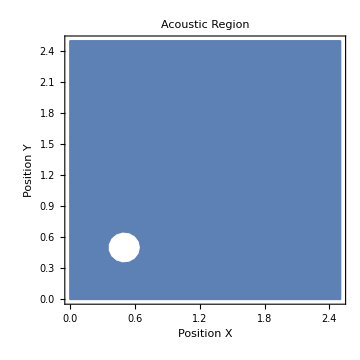

```mathematica
r=2.5;
Ω=RegionDifference[Rectangle[{0,0},{r,r}],Disk[{0.5,0.5},r/16]];
RegionPlot[Ω,]
```

CodeTextInfoButtonDescribe your concepts in a few sentences of text.
	◼ Text describes the flow of conversation.
	◼ It clarifies the transition from one segment to the next one.
	◼ It should explain how the topic is studied and (broadly) how the topic is implemented in the code.

Examples:
	Find the eigenvalues:
	A function that generates a two-dimensional graphic of an n x m array of cells with value 1:Click for more informationDefining the sound source and boundary conditions:

```mathematica
xs = 1.25;
ys=1.25;
```

```mathematica
monopoleModel2D=AcousticModel[p[x,y],{x,y},ρ,{Q[ω,{x,y},{xs,ys}],{0}}]-(ω^2 p[x,y])/(ρ c^2);
```

```mathematica
Subscript[Γ, abcf]=NeumannValue[-(((ⅈ ω)/c+1/(2 r)) p[x,y])/ρ,True];
```

CodeTextInfoButtonDescribe your concepts in a few sentences of text.
	◼ Text describes the flow of conversation.
	◼ It clarifies the transition from one segment to the next one.
	◼ It should explain how the topic is studied and (broadly) how the topic is implemented in the code.

Examples:
	Find the eigenvalues:
	A function that generates a two-dimensional graphic of an n x m array of cells with value 1:Click for more informationDefining the PDE and solving it with ParametricNDSolve:

```mathematica
pde={monopoleModel2D==Subscript[Γ, abcf]}/.{c->Subscript[c, air],ρ->Subscript[ρ, air]};
pfunMonopole2D=ParametricNDSolveValue[pde,p,{x,y}∈Ω,{ω},AcousticsOptions[Subscript[c, air],ω]]
```

ParametricFunction[<>]

CodeTextInfoButtonDescribe your concepts in a few sentences of text.
	◼ Text describes the flow of conversation.
	◼ It clarifies the transition from one segment to the next one.
	◼ It should explain how the topic is studied and (broadly) how the topic is implemented in the code.

Examples:
	Find the eigenvalues:
	A function that generates a two-dimensional graphic of an n x m array of cells with value 1:Click for more informationVisualizing Pressure in the Region at 500Hz with a Monopole Sound Source in 2D:

```mathematica
(*pMonopole500Hz=pfunMonopole2D[2 π f/.{f->500}]*);
```

```mathematica
(*Viz500Hz=Legended[ContourPlot[Abs[pMonopole500Hz[x,y]],{x,y}∈Ω,],]*)
```

```mathematica
Import["Desktop/git-repos/Wolfram-Spatial-Audio/Graphics/2dPressureFreq500HzLTC.png"]
```

-Graphics-

CodeTextInfoButtonDescribe your concepts in a few sentences of text.
	◼ Text describes the flow of conversation.
	◼ It clarifies the transition from one segment to the next one.
	◼ It should explain how the topic is studied and (broadly) how the topic is implemented in the code.

Examples:
	Find the eigenvalues:
	A function that generates a two-dimensional graphic of an n x m array of cells with value 1:Click for more informationVisualizing Pressure in the Region between 100Hz and 1000Hz with a Monopole Sound Source in 2D:

## SectionHeaderInfoButtonA proper heading structure helps to organize your content for readability. ◼ Categorize sections based on similar content. ◼ Each section should tell a story by itself. ◼ Headings overall should tell the outline of the essay. Examples: The Central Limit Theorem Discovering the Central Limit Theorem The Normal Distribution Toward the Normal Distribution The Normal Distribution in 2D and Beyond Random Walks What Is Not a Normal Distribution Collapse Models Collapse Problem in Quantum Random Processes Collapse as a Dynamical Random Process Recovering Quantum after Statistical Averaging Drawbacks of Collapse Models Click for more informationUsing Acoustic Models to Modify Audio

TopicSentenceInfoButtonDescribe your concepts in a few sentences of text.
	◼ Text describes the flow of conversation.
	◼ It clarifies the transition from one segment to the next one.
	◼ It should explain how the topic is studied and (broadly) how the topic is implemented in the code.Click for more informationHaving modeled the acoustics for different regions in both the time and frequency domain,

CodeTextInfoButtonDescribe your concepts in a few sentences of text.
	◼ Text describes the flow of conversation.
	◼ It clarifies the transition from one segment to the next one.
	◼ It should explain how the topic is studied and (broadly) how the topic is implemented in the code.

Examples:
	Find the eigenvalues:
	A function that generates a two-dimensional graphic of an n x m array of cells with value 1:Click for more informationApplying a Short Term Fourier Transform to

```mathematica
XXXX CodeInfoButtonCode should be clear, easy to read and ideally no more than three lines long. 
	◼ Avoid long, overly complex blocks of code.
	◼ Break complicated, lengthy code into multiple segments.
	◼ CodeText should precede each code segment. 
	◼ All Manipulate functions should be self-contained. Use Initialization and/or SaveDefinitions.
	◼ If it is a repeated function, give it a Wolfram Function Repository page.Click for more information
```

XXXXVisualisationInfoButtonInclude simple visualizations to illustrate the topic and engage the reader in the discussion. 
	◼ Visualizations should work well and contribute to the narrative.
	◼ Visualizations, together with interactivity, should convey the topic effectively. 
		◼ A non-expert should be able to read the essay and understand something new.
	◼ Visualizations must be self-explanatory.
		◼ Add captions, legends, callouts, etc.
		◼ Label axes, explicitly mentioning any units/dimensions.
		◼ Label the overall plot.Click for more information

## SectionHeaderInfoButtonA proper heading structure helps to organize your content for readability. ◼ Categorize sections based on similar content. ◼ Each section should tell a story by itself. ◼ Headings overall should tell the outline of the essay. Examples: The Central Limit Theorem Discovering the Central Limit Theorem The Normal Distribution Toward the Normal Distribution The Normal Distribution in 2D and Beyond Random Walks What Is Not a Normal Distribution Collapse Models Collapse Problem in Quantum Random Processes Collapse as a Dynamical Random Process Recovering Quantum after Statistical Averaging Drawbacks of Collapse Models Click for more informationConclusion

TopicSentenceInfoButtonDescribe your concepts in a few sentences of text.
	◼ Text describes the flow of conversation.
	◼ It clarifies the transition from one segment to the next one.
	◼ It should explain how the topic is studied and (broadly) how the topic is implemented in the code.Click for more information

XXXX:CodeTextInfoButtonDescribe your concepts in a few sentences of text.
	◼ Text describes the flow of conversation.
	◼ It clarifies the transition from one segment to the next one.
	◼ It should explain how the topic is studied and (broadly) how the topic is implemented in the code.

Examples:
	Find the eigenvalues:
	A function that generates a two-dimensional graphic of an n x m array of cells with value 1:Click for more information

```mathematica
XXXX CodeInfoButtonCode should be clear, easy to read and ideally no more than three lines long. 
	◼ Avoid long, overly complex blocks of code.
	◼ Break complicated, lengthy code into multiple segments.
	◼ CodeText should precede each code segment. 
	◼ All Manipulate functions should be self-contained. Use Initialization and/or SaveDefinitions.
	◼ If it is a repeated function, give it a Wolfram Function Repository page.Click for more information
```

XXXXVisualisationInfoButtonInclude simple visualizations to illustrate the topic and engage the reader in the discussion. 
	◼ Visualizations should work well and contribute to the narrative.
	◼ Visualizations, together with interactivity, should convey the topic effectively. 
		◼ A non-expert should be able to read the essay and understand something new.
	◼ Visualizations must be self-explanatory.
		◼ Add captions, legends, callouts, etc.
		◼ Label axes, explicitly mentioning any units/dimensions.
		◼ Label the overall plot.Click for more information

## KeywordsKeywordsInfoButtonList relevant terms that should be used to include the essay in search results.Click for more information